```mathematica
0.275*11.5
```

3.1625

```mathematica
UnitConvert[Quantity["11.5 Meter^-2"]*Quantity["50 MeV/c"]/Quantity["e"],"Tesla/Meter"]*Quantity["0.275 Meter"]
```

0.527 T

```mathematica
<<astrainterpret`
```

```mathematica
SetDirectory["c:\\temp\\262k_particles"];
```

```mathematica
SetDirectory["C:\\anaconda32\\Work\\Online-Model\\ASTRAFramework\\ASTRAGeneral\\2"];
```

```mathematica
FileNames["short_240.5.*.*"]
```

{short_240.5.3285.001,short_240.5.3390.001,short_240.5.3985.001,short_240.5.4258.001,short_240.5.4403.001,short_240.5.4636.001,short_240.5.4778.001,short_240.5.4918.001,short_240.5.4936.001,short_240.5.Log.001,short_240.5.Xemit.001,short_240.5.Yemit.001,short_240.5.Zemit.001}

```mathematica
ASTRABeamInterpret["short_240.5.3985.001"]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

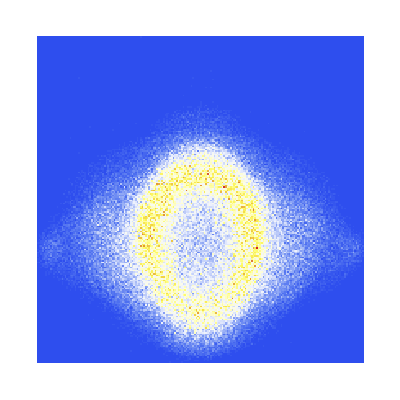

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=x;
Yaxis=y;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/200},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/200}],ColorFunction->"TemperatureMap"]
]
```

```mathematica
FileNames["short_240.2.*.001"]
```

{short_240.2.0409.001,short_240.2.0501.001,short_240.2.0658.001,short_240.2.1191.001,short_240.2.1620.001,short_240.2.Xemit.001,short_240.2.Yemit.001,short_240.2.Zemit.001}

```mathematica
ASTRABeamInterpret[FileNames["short_240.2.*.001"][[1]]]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

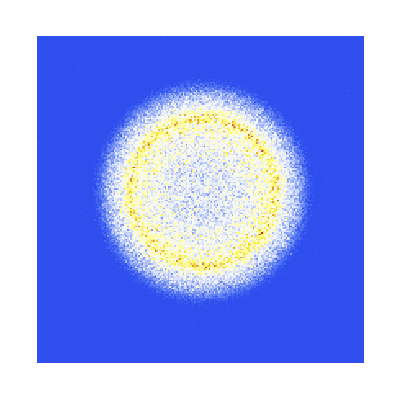

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=x;
Yaxis=y;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/200},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/200}],ColorFunction->"TemperatureMap"]
]
```

```mathematica
FileNames["short_240.1.*.001"]
```

{short_240.1.0098.001,short_240.1.0337.001,short_240.1.Xemit.001,short_240.1.Yemit.001,short_240.1.Zemit.001}

```mathematica
ASTRABeamInterpret[FileNames["short_240.1.*.001"][[2]]]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

```mathematica
NIntegrate
```

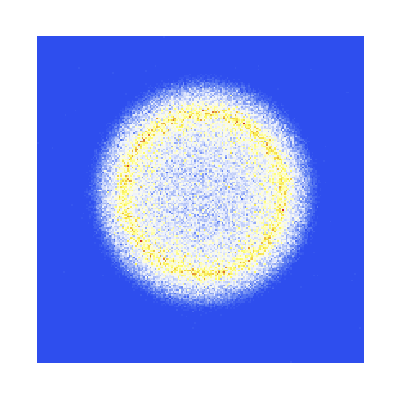

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=x;
Yaxis=y;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/200},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/200}],ColorFunction->"TemperatureMap"]
]
```

```mathematica
ASTRAemitInterpret["short_240."<>ToString[#]<>".Zemit.001"&/@Range[5]]
```

ReadList::noopen: Cannot open short_240.1.Xemit.001.

ReadList::noopen: Cannot open short_240.2.Xemit.001.

ReadList::noopen: Cannot open short_240.3.Xemit.001.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {$Failed,$Failed,$Failed,$Failed,$Failed} cannot be transposed.

Transpose::nmtx: The first two levels of {{{z,1,Number},{t,1,Number},{xavr,1,Number},{xrms,1,Number},{xprms,1,Number},{ϵxnorm,1,Number},{xxpavr,1,Number}},Transpose[{$Failed,$Failed,$Failed,$Failed,$Failed}]} cannot be transposed.

StringJoin::string: String expected at position 2 in z<>(1)<>Number.

StringJoin::string: String expected at position 3 in z<>(1)<>Number.

Clear::ssym: z<>(1)<>Number is not a symbol or a string.

StringJoin::string: String expected at position 2 in z<>(1)<>Number.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[z<>(1)<>Number].

Set::write: Tag Symbol in Symbol[z<>(1)<>Number] is Protected.

Transpose::nmtx: The first two levels of {$Failed,$Failed,$Failed,$Failed,$Failed} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Clear::ssym: z<>(1)<>Number is not a symbol or a string.

Symbol::string: String expected at position 1 in Symbol[z<>(1)<>Number].

Set::write: Tag Symbol in Symbol[z<>(1)<>Number] is Protected.

Clear::ssym: z<>(1)<>Number is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[z<>(1)<>Number].

General::stop: Further output of Symbol::string will be suppressed during this calculation.

Set::write: Tag Symbol in Symbol[z<>(1)<>Number] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
ListLinePlot[Sort/@{Transpose[{z,xrms}],Transpose[{z,yrms}]},PlotRange->All]
```

Transpose::nmtx: The first two levels of {{3.37151,3.37173,3.37128,3.37194,3.37105,3.37214,3.37084,3.37077,3.37162,3.37094,3.37117,3.37115,3.37174,3.371,3.37151,3.37114,3.37193,3.37082,3.3707,3.37103,3.37189,3.37134,3.37088,3.37192,3.37082,«19»,«19»,3.37112,3.3715,3.37144,3.37144,3.37094,3.37134,3.37093,3.37211,3.37214,3.37088,3.37147,3.37187,3.37152,3.37165,3.37168,3.37186,3.37142,3.37135,3.37219,3.37186,3.37116,3.37204,3.37122,«32718»},{«1»}} cannot be transposed.

-Graphics-

#### Framework

```mathematica
Clear[z,xrms,yrms]
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Online-Model\\ASTRAFramework\\ASTRAGeneral\\"];
```

```mathematica
dirs=FileNames["tmp*",{"\\\\apclara1\\jkj62\\Online-Model\\ASTRAFramework\\ASTRAGeneral\\"}]
```

{}

```mathematica
SetDirectory[dirs[[1]]]
```

Part::partw: Part 1 of {} does not exist.

SetDirectory::fstr: File specification {}⟦1⟧ is not a string of one or more characters.

SetDirectory[{}⟦1⟧]

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Online-Model\\ASTRAFramework\\ASTRAGeneral\\test_transverse"];
```

```mathematica
files={"../twiss_temp/Injector400","S02","L02","S03","L03","S04","L4H","S05","S06","L04","S07"};
```

```mathematica
ASTRAemitInterpret[If[FileExistsQ["./"<>ToString[#]<>".Zemit.001"]&&FileByteCount["./"<>ToString[#]<>".Zemit.001"]>10000,"./"<>ToString[#]<>".Zemit.001",Nothing]&/@files]
```

```mathematica
Length[z]
Max[z]
```

6271

23.194

```mathematica
Length[xrms]
```

6260

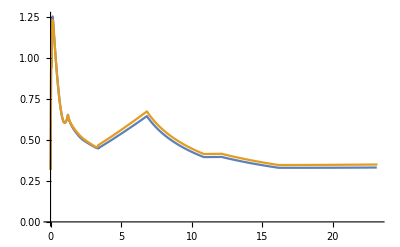

```mathematica
If[Length[z]>Length[xrms],
ListLinePlot[Sort/@{Transpose[{z[[1;;Length[xrms]]],xrms}],Transpose[{z[[1;;Length[yrms]]],yrms}]},PlotRange->All],
ListLinePlot[Sort/@{Transpose[{z,xrms[[1;;Length[z]]]}],Transpose[{z,yrms[[1;;Length[z]]]}]},PlotRange->All]
]
```

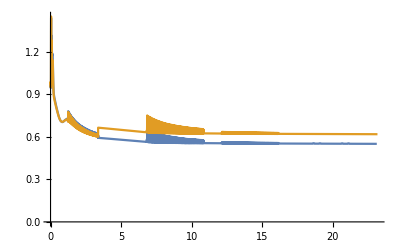

```mathematica
If[Length[z]>Length[ϵxnorm],
ListLinePlot[Sort/@{Transpose[{z[[1;;Length[ϵxnorm]]],ϵxnorm}],Transpose[{z[[1;;Length[ϵynorm]]],ϵynorm}]},PlotRange->All],
ListLinePlot[Sort/@{Transpose[{z,ϵxnorm[[1;;Length[z]]]}],Transpose[{z,ϵynorm[[1;;Length[z]]]}]},PlotRange->All]
]
```

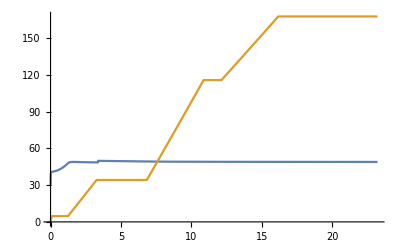

```mathematica
ListLinePlot[Sort/@{Transpose[{z[[1;;Length[zrms]]],100zrms}],Transpose[{z[[1;;Length[Ekin]]],Ekin}]},PlotRange->All]
```

```mathematica
ListLinePlot[Sort/@{Transpose[{z[[1;;Length[ϵxnorm ϵynorm ϵznorm]]],10ϵxnorm ϵynorm ϵznorm}],Transpose[{z[[1;;Length[Ekin]]],Ekin}]},PlotRange->All]
```

Thread::tdlen: Objects of unequal length in {0.95404,0.97451,0.96091,0.94308,0.94312,0.95429,0.95788,0.95484,1.011,1.1705,1.3425,1.4348,1.4316,1.3558,1.2466,1.125,1.0411,1.0164,1.0692,1.1545,1.1794,1.1015,0.99679,1.0284,1.1515,1.2562,1.3091,1.3111,1.2689,1.2259,1.1981,1.1847,1.1778,1.1739,1.1718,1.1713,1.1717,1.173,1.175,1.1775,1.18,1.1825,1.184,1.1844,1.1832,1.1801,1.1746,1.1672,1.1577,1.1453,«6210»} {«1»} {0.36953,0.61641,0.78346,0.90916,1.022,1.1228,1.2284,1.3288,1.4115,1.481,1.5303,1.5679,1.5989,1.6319,1.6619,1.6912,1.7158,1.7419,1.7652,1.7921,1.8175,1.8408,1.8613,1.8773,1.8929,1.9105,1.9272,1.9456,1.9639,1.9812,1.998,2.013,2.0276,2.0427,2.0567,2.0714,2.0842,2.0968,2.1101,2.1223,2.1343,2.1469,2.1583,2.1703,2.1813,2.1921,2.2035,2.214,2.2244,2.2354,«6221»} cannot be combined.

Thread::tdlen: Objects of unequal length in 10 {0.95404,0.97451,0.96091,0.94308,0.94312,0.95429,0.95788,0.95484,1.011,1.1705,1.3425,1.4348,1.4316,1.3558,1.2466,1.125,1.0411,1.0164,1.0692,1.1545,1.1794,1.1015,0.99679,1.0284,1.1515,1.2562,1.3091,1.3111,1.2689,1.2259,1.1981,1.1847,1.1778,1.1739,1.1718,1.1713,1.1717,1.173,1.175,1.1775,1.18,1.1825,1.184,1.1844,1.1832,1.1801,1.1746,1.1672,1.1577,1.1453,«6210»} {«1»} {0.36953,0.61641,0.78346,0.90916,1.022,1.1228,1.2284,1.3288,1.4115,1.481,1.5303,1.5679,1.5989,1.6319,1.6619,1.6912,1.7158,1.7419,1.7652,1.7921,1.8175,1.8408,1.8613,1.8773,1.8929,1.9105,1.9272,1.9456,1.9639,1.9812,1.998,2.013,2.0276,2.0427,2.0567,2.0714,2.0842,2.0968,2.1101,2.1223,2.1343,2.1469,2.1583,2.1703,2.1813,2.1921,2.2035,2.214,2.2244,2.2354,«6221»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.0029466,0.0062021,0.009495},10 {0.95404,0.97451,0.96091,0.94308,0.94312,0.95429,0.95788,0.95484,1.011,1.1705,1.3425,1.4348,1.4316,1.3558,1.2466,1.125,1.0411,1.0164,1.0692,1.1545,1.1794,1.1015,0.99679,«5»,1.2689,1.2259,1.1981,1.1847,1.1778,1.1739,1.1718,1.1713,1.1717,1.173,1.175,1.1775,1.18,1.1825,1.184,1.1844,1.1832,1.1801,1.1746,1.1672,1.1577,1.1453,«6210»} {«1»} {0.36953,0.61641,0.78346,0.90916,1.022,1.1228,1.2284,1.3288,1.4115,1.481,1.5303,1.5679,1.5989,1.6319,1.6619,1.6912,1.7158,1.7419,1.7652,1.7921,1.8175,1.8408,1.8613,1.8773,1.8929,1.9105,1.9272,1.9456,1.9639,1.9812,1.998,2.013,2.0276,2.0427,2.0567,2.0714,2.0842,2.0968,2.1101,2.1223,2.1343,2.1469,2.1583,2.1703,2.1813,2.1921,2.2035,2.214,2.2244,2.2354,«6221»}} cannot be transposed.

Thread::tdlen: Objects of unequal length in 10. {0.95404,0.97451,0.96091,0.94308,0.94312,0.95429,0.95788,0.95484,1.011,1.1705,1.3425,1.4348,1.4316,1.3558,1.2466,1.125,1.0411,1.0164,1.0692,1.1545,1.1794,1.1015,0.99679,1.0284,1.1515,1.2562,1.3091,1.3111,1.2689,1.2259,1.1981,1.1847,1.1778,1.1739,1.1718,1.1713,1.1717,1.173,1.175,1.1775,1.18,1.1825,1.184,1.1844,1.1832,1.1801,1.1746,1.1672,1.1577,1.1453,«6210»} {«1»} {0.36953,0.61641,0.78346,0.90916,1.022,1.1228,1.2284,1.3288,1.4115,1.481,1.5303,1.5679,1.5989,1.6319,1.6619,1.6912,1.7158,1.7419,1.7652,1.7921,1.8175,1.8408,1.8613,1.8773,1.8929,1.9105,1.9272,1.9456,1.9639,1.9812,1.998,2.013,2.0276,2.0427,2.0567,2.0714,2.0842,2.0968,2.1101,2.1223,2.1343,2.1469,2.1583,2.1703,2.1813,2.1921,2.2035,2.214,2.2244,2.2354,«6221»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted[]

$Aborted[]

```mathematica
FileNames["*",{"../twiss_temp"}]
```

{../twiss_temp\33k-250pC.ini,../twiss_temp\4k-250pC.ini,../twiss_temp\generator.in,../twiss_temp\injector400.0098.001,../twiss_temp\injector400.0337.001,../twiss_temp\injector400.in,../twiss_temp\injector400.Log.001,../twiss_temp\injector400.ref.001,../twiss_temp\injector400.track.001,../twiss_temp\injector400.Xemit.001,../twiss_temp\injector400.Yemit.001,../twiss_temp\injector400.Zemit.001,../twiss_temp\L02.in,../twiss_temp\L03.in,../twiss_temp\L04.in,../twiss_temp\L4H.in,../twiss_temp\NORRAN,../twiss_temp\S02.in,../twiss_temp\S03.in,../twiss_temp\S04.in,../twiss_temp\S05.in,../twiss_temp\S06.in,../twiss_temp\S07.in,../twiss_temp\VBC.in}

```mathematica
beamfiles=Select[FileNames["*",{"../twiss_temp"}],StringMatchQ[#,"*injector400."~~DigitCharacter..~~".001"]&]
```

{../twiss_temp\injector400.0098.001,../twiss_temp\injector400.0337.001}

```mathematica
ASTRABeamInterpret["./"<>beamfiles[[1]]]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

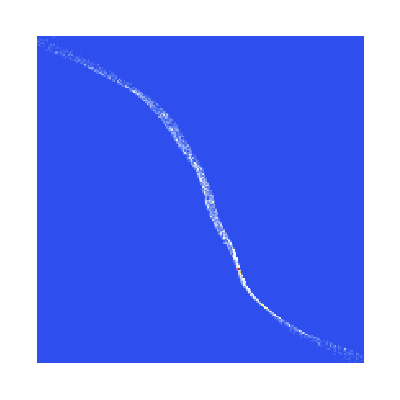

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=z;
Yaxis=pz;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/200},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/200}],ColorFunction->"TemperatureMap"]
]
```

```mathematica
beamfiles=Select[FileNames["*"],StringMatchQ[#,"S07."~~DigitCharacter..~~".001"]&]
```

{S07.3993.001,S07.4266.001,S07.4644.001,S07.4787.001,S07.4910.001,S07.4928.001}

```mathematica
ASTRABeamInterpret["./"<>beamfiles[[1]]]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

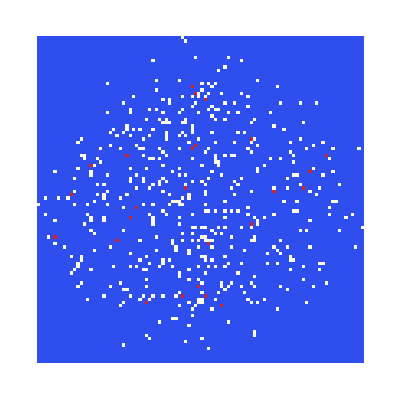

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=x;
Yaxis=y;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/100},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/100}],ColorFunction->"TemperatureMap"]
]
```

### JWM Sims

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC-TDL\\Projects\\tdl-1168 CLARA\\acc - accelerator physics (WP9)\\ASTRA\\Injector\\250-MC-10"]
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC-TDL\Projects\tdl-1168 CLARA\acc - accelerator physics (WP9)\ASTRA\Injector\250-MC-10

```mathematica
files={"250-MC-10"};
```

```mathematica
ASTRAemitInterpret["./"<>ToString[#]<>".Zemit.001"&/@files]
```

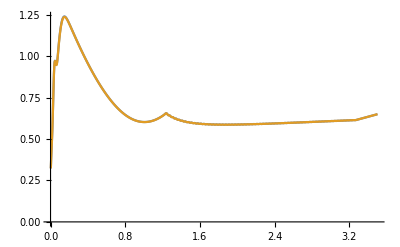

```mathematica
ListLinePlot[Sort/@{Transpose[{z,xrms}],Transpose[{z,yrms}]},PlotRange->All]
```

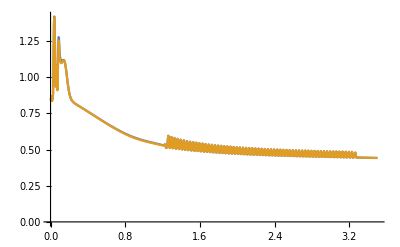

```mathematica
ListLinePlot[Sort/@{Transpose[{z,ϵxnorm}],Transpose[{z,ϵynorm}]},PlotRange->All]
```

```mathematica
beamfiles=Select[FileNames["250-MC-10.*.001"],StringMatchQ[#,"250-MC-10."~~DigitCharacter..~~".001"]&]
```

{250-MC-10.0350.001}

```mathematica
ASTRABeamInterpret["./"<>beamfiles[[1]],ASTRAVerbose->True]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

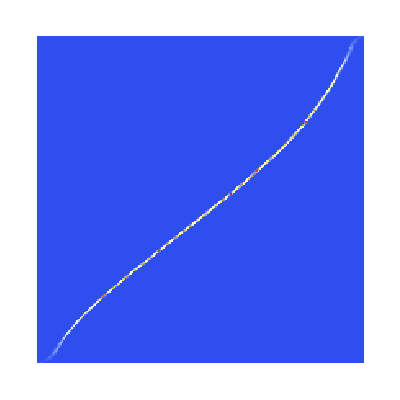

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=z;
Yaxis=pz;
ArrayPlot[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/200},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/200}],ColorFunction->"TemperatureMap"]
]
```

```mathematica
Block[{Xaxis,Yaxis},
Xaxis=x;
Yaxis=y;
ListPlot3D[BinCounts[Transpose[{Xaxis,Yaxis}],{Min[Xaxis],Max[Xaxis],(Max[Xaxis]-Min[Xaxis])/25},{Min[Yaxis],Max[Yaxis],(Max[Yaxis]-Min[Yaxis])/25}],ColorFunction->"TemperatureMap",PlotRange->All]
]
```

-Graphics3D-

```mathematica
2^(3*5)/2^(3*4)
```

8

## Sol Analysis

```mathematica
gunsol=Import["\\\\apclara1\\jkj62\\Online-Model\\MasterLattice\\Data_Files\\HRRG_combined_sols_100mm_onaxis.dat"];
```

```mathematica
gunsol
```

{{-0.251,0.},{-0.25,-0.000686454},{-0.249,-0.000703084},{-0.248,-0.000720113},{-0.247,-0.000737551},{-0.246,-0.00075541},{-0.245,-0.000773703},{-0.244,-0.000792442},{-0.243,-0.00081164},{-0.242,-0.000831312},{-0.241,-0.000851472},{-0.24,-0.000872135},{-0.239,-0.000893316},{-0.238,-0.000915032},{-0.237,-0.000937299},{-0.236,-0.000960135},{-0.235,-0.000983558},{-0.234,-0.00100759},{-0.233,-0.00103224},{-0.232,-0.00105754},{-0.231,-0.00108351},{-0.23,-0.00111017},{-0.229,-0.00113755},{-0.228,-0.00116566},{-0.227,-0.00119453},{-0.226,-0.0012242},{-0.225,-0.00125469},{-0.224,-0.00128602},{-0.223,-0.00131823},{-0.222,-0.00135135},{-0.221,-0.00138542},{-0.22,-0.00142046},{-0.219,-0.00145652},{-0.218,-0.00149363},{-0.217,-0.00153183},{-0.216,-0.00157118},{-0.215,-0.0016117},{-0.214,-0.00165345},{-0.213,-0.00169647},{-0.212,-0.00174082},{-0.211,-0.00178655},{-0.21,-0.00183372},{-0.209,-0.00188238},{-0.208,-0.0019326},{-0.207,-0.00198444},{-0.206,-0.00203797},{-0.205,-0.00209327},{-0.204,-0.0021504},{-0.203,-0.00220945},{-0.202,-0.00227051},{-0.201,-0.00233365},{-0.2,-0.00239897},{-0.199,-0.00246657},{-0.198,-0.00253656},{-0.197,-0.00260903},{-0.196,-0.0026841},{-0.195,-0.00276189},{-0.194,-0.00284252},{-0.193,-0.00292612},{-0.192,-0.00301284},{-0.191,-0.00310281},{-0.19,-0.00319619},{-0.189,-0.00329314},{-0.188,-0.00339381},{-0.187,-0.0034984},{-0.186,-0.00360708},{-0.185,-0.00372005},{-0.184,-0.0038375},{-0.183,-0.00395965},{-0.182,-0.00408673},{-0.181,-0.00421896},{-0.18,-0.00435658},{-0.179,-0.00449986},{-0.178,-0.00464906},{-0.177,-0.00480445},{-0.176,-0.00496633},{-0.175,-0.005135},{-0.174,-0.00531077},{-0.173,-0.00549398},{-0.172,-0.00568497},{-0.171,-0.00588409},{-0.17,-0.00609171},{-0.169,-0.00630822},{-0.168,-0.00653402},{-0.167,-0.00676952},{-0.166,-0.00701516},{-0.165,-0.00727138},{-0.164,-0.00753863},{-0.163,-0.00781739},{-0.162,-0.00810815},{-0.161,-0.00841142},{-0.16,-0.00872772},{-0.159,-0.00905758},{-0.158,-0.00940155},{-0.157,-0.00976021},{-0.156,-0.0101341},{-0.155,-0.0105239},{-0.154,-0.0109301},{-0.153,-0.0113534},{-0.152,-0.0117945},{-0.151,-0.0122539},{-0.15,-0.0127324},{-0.149,-0.0132305},{-0.148,-0.0137491},{-0.147,-0.0142888},{-0.146,-0.0148503},{-0.145,-0.0154344},{-0.144,-0.0160417},{-0.143,-0.0166731},{-0.142,-0.0173292},{-0.141,-0.018011},{-0.14,-0.018719},{-0.139,-0.0194542},{-0.138,-0.0202174},{-0.137,-0.0210093},{-0.136,-0.0218308},{-0.135,-0.0226827},{-0.134,-0.0235659},{-0.133,-0.0244811},{-0.132,-0.0254294},{-0.131,-0.0264116},{-0.13,-0.0274285},{-0.129,-0.0284811},{-0.128,-0.0295703},{-0.127,-0.030697},{-0.126,-0.0318622},{-0.125,-0.0330668},{-0.124,-0.0343117},{-0.123,-0.035598},{-0.122,-0.0369266},{-0.121,-0.0382986},{-0.12,-0.0397149},{-0.119,-0.0411765},{-0.118,-0.0426845},{-0.117,-0.0442398},{-0.116,-0.0458436},{-0.115,-0.0474968},{-0.114,-0.0492004},{-0.113,-0.0509556},{-0.112,-0.0527632},{-0.111,-0.0546243},{-0.11,-0.0565398},{-0.109,-0.0585108},{-0.108,-0.0605382},{-0.107,-0.0626229},{-0.106,-0.0647657},{-0.105,-0.0669675},{-0.104,-0.069229},{-0.103,-0.071551},{-0.102,-0.0739341},{-0.101,-0.0763789},{-0.1,-0.0788858},{-0.099,-0.0814553},{-0.098,-0.0840877},{-0.097,-0.0867831},{-0.096,-0.0895415},{-0.095,-0.0923629},{-0.094,-0.095247},{-0.093,-0.0981934},{-0.092,-0.101202},{-0.091,-0.104271},{-0.09,-0.107399},{-0.089,-0.110587},{-0.088,-0.113832},{-0.087,-0.117132},{-0.086,-0.120486},{-0.085,-0.123891},{-0.084,-0.127345},{-0.083,-0.130845},{-0.082,-0.134388},{-0.081,-0.137971},{-0.08,-0.141588},{-0.079,-0.145238},{-0.078,-0.148914},{-0.077,-0.152612},{-0.076,-0.156327},{-0.075,-0.160054},{-0.074,-0.163785},{-0.073,-0.167516},{-0.072,-0.171239},{-0.071,-0.174948},{-0.07,-0.178634},{-0.069,-0.182291},{-0.068,-0.18591},{-0.067,-0.189483},{-0.066,-0.193002},{-0.065,-0.196457},{-0.064,-0.199839},{-0.063,-0.20314},{-0.062,-0.20635},{-0.061,-0.20946},{-0.06,-0.212459},{-0.059,-0.215338},{-0.058,-0.218088},{-0.057,-0.220698},{-0.056,-0.223159},{-0.055,-0.225463},{-0.054,-0.227598},{-0.053,-0.229557},{-0.052,-0.231331},{-0.051,-0.23291},{-0.05,-0.234287},{-0.049,-0.235454},{-0.048,-0.236404},{-0.047,-0.237129},{-0.046,-0.237623},{-0.045,-0.23788},{-0.044,-0.237894},{-0.043,-0.237661},{-0.042,-0.237176},{-0.041,-0.236436},{-0.04,-0.235436},{-0.039,-0.234176},{-0.038,-0.232651},{-0.037,-0.230862},{-0.036,-0.228807},{-0.035,-0.226486},{-0.034,-0.2239},{-0.033,-0.221048},{-0.032,-0.217932},{-0.031,-0.214554},{-0.03,-0.210916},{-0.029,-0.207021},{-0.028,-0.202871},{-0.027,-0.19847},{-0.026,-0.193822},{-0.025,-0.188931},{-0.024,-0.1838},{-0.023,-0.178434},{-0.022,-0.172837},{-0.021,-0.167015},{-0.02,-0.160972},{-0.019,-0.154713},{-0.018,-0.148242},{-0.017,-0.141565},{-0.016,-0.134687},{-0.015,-0.127611},{-0.014,-0.120344},{-0.013,-0.112889},{-0.012,-0.105252},{-0.011,-0.097436},{-0.01,-0.0894459},{-0.009,-0.0812857},{-0.008,-0.0729592},{-0.007,-0.0644703},{-0.006,-0.0558224},{-0.005,-0.0470189},{-0.004,-0.038063},{-0.003,-0.0289577},{-0.002,-0.0197056},{-0.001,-0.0103095},{0.,-0.000771629},{0.001,0.00890562},{0.002,0.0187202},{0.003,0.0286702},{0.004,0.0387537},{0.005,0.0489691},{0.006,0.0593148},{0.007,0.0697893},{0.008,0.0803912},{0.009,0.0911192},{0.01,0.101972},{0.011,0.112948},{0.012,0.124046},{0.013,0.135264},{0.014,0.146602},{0.015,0.158058},{0.016,0.16963},{0.017,0.181317},{0.018,0.193116},{0.019,0.205026},{0.02,0.217046},{0.021,0.229172},{0.022,0.241402},{0.023,0.253734},{0.024,0.266164},{0.025,0.27869},{0.026,0.291308},{0.027,0.304015},{0.028,0.316806},{0.029,0.329678},{0.03,0.342625},{0.031,0.355644},{0.032,0.368729},{0.033,0.381875},{0.034,0.395076},{0.035,0.408326},{0.036,0.421619},{0.037,0.434948},{0.038,0.448307},{0.039,0.461688},{0.04,0.475084},{0.041,0.488488},{0.042,0.501891},{0.043,0.515285},{0.044,0.528663},{0.045,0.542016},{0.046,0.555334},{0.047,0.568609},{0.048,0.581833},{0.049,0.594996},{0.05,0.608088},{0.051,0.621102},{0.052,0.634026},{0.053,0.646853},{0.054,0.659572},{0.055,0.672175},{0.056,0.684652},{0.057,0.696993},{0.058,0.70919},{0.059,0.721234},{0.06,0.733116},{0.061,0.744826},{0.062,0.756357},{0.063,0.767699},{0.064,0.778845},{0.065,0.789786},{0.066,0.800515},{0.067,0.811024},{0.068,0.821305},{0.069,0.831352},{0.07,0.841157},{0.071,0.850714},{0.072,0.860016},{0.073,0.869058},{0.074,0.877834},{0.075,0.886337},{0.076,0.894563},{0.077,0.902507},{0.078,0.910164},{0.079,0.91753},{0.08,0.9246},{0.081,0.93137},{0.082,0.937838},{0.083,0.943999},{0.084,0.94985},{0.085,0.955388},{0.086,0.960612},{0.087,0.965517},{0.088,0.970103},{0.089,0.974368},{0.09,0.978308},{0.091,0.981924},{0.092,0.985213},{0.093,0.988174},{0.094,0.990807},{0.095,0.993111},{0.096,0.995085},{0.097,0.996728},{0.098,0.998042},{0.099,0.999025},{0.1,0.999677},{0.101,1.},{0.102,0.999993},{0.103,0.999658},{0.104,0.998995},{0.105,0.998004},{0.106,0.996689},{0.107,0.995049},{0.108,0.993086},{0.109,0.990803},{0.11,0.9882},{0.111,0.985281},{0.112,0.982048},{0.113,0.978503},{0.114,0.974649},{0.115,0.970489},{0.116,0.966027},{0.117,0.961265},{0.118,0.956208},{0.119,0.95086},{0.12,0.945224},{0.121,0.939305},{0.122,0.933108},{0.123,0.926639},{0.124,0.919901},{0.125,0.912901},{0.126,0.905645},{0.127,0.898138},{0.128,0.890386},{0.129,0.882398},{0.13,0.874178},{0.131,0.865736},{0.132,0.857077},{0.133,0.848209},{0.134,0.839141},{0.135,0.82988},{0.136,0.820436},{0.137,0.810816},{0.138,0.801029},{0.139,0.791085},{0.14,0.780992},{0.141,0.77076},{0.142,0.760398},{0.143,0.749916},{0.144,0.739324},{0.145,0.728631},{0.146,0.717848},{0.147,0.706984},{0.148,0.69605},{0.149,0.685054},{0.15,0.674008},{0.151,0.662921},{0.152,0.651803},{0.153,0.640664},{0.154,0.629514},{0.155,0.618361},{0.156,0.607216},{0.157,0.596087},{0.158,0.584984},{0.159,0.573915},{0.16,0.56289},{0.161,0.551916},{0.162,0.541001},{0.163,0.530154},{0.164,0.519381},{0.165,0.508691},{0.166,0.49809},{0.167,0.487584},{0.168,0.47718},{0.169,0.466884},{0.17,0.456701},{0.171,0.446637},{0.172,0.436697},{0.173,0.426885},{0.174,0.417205},{0.175,0.407661},{0.176,0.398257},{0.177,0.388996},{0.178,0.379881},{0.179,0.370914},{0.18,0.362098},{0.181,0.353434},{0.182,0.344924},{0.183,0.33657},{0.184,0.328371},{0.185,0.32033},{0.186,0.312447},{0.187,0.304721},{0.188,0.297154},{0.189,0.289743},{0.19,0.28249},{0.191,0.275393},{0.192,0.268452},{0.193,0.261666},{0.194,0.255033},{0.195,0.248552},{0.196,0.242221},{0.197,0.236039},{0.198,0.230005},{0.199,0.224115},{0.2,0.218369},{0.201,0.212764},{0.202,0.207298},{0.203,0.201969},{0.204,0.196774},{0.205,0.191711},{0.206,0.186779},{0.207,0.181973},{0.208,0.177293},{0.209,0.172735},{0.21,0.168296},{0.211,0.163976},{0.212,0.15977},{0.213,0.155676},{0.214,0.151692},{0.215,0.147816},{0.216,0.144044},{0.217,0.140375},{0.218,0.136805},{0.219,0.133333},{0.22,0.129956},{0.221,0.126671},{0.222,0.123477},{0.223,0.12037},{0.224,0.11735},{0.225,0.114412},{0.226,0.111556},{0.227,0.108779},{0.228,0.106079},{0.229,0.103453},{0.23,0.100901},{0.231,0.0984187},{0.232,0.0960055},{0.233,0.0936591},{0.234,0.0913778},{0.235,0.0891595},{0.236,0.0870027},{0.237,0.0849054},{0.238,0.0828661},{0.239,0.080883},{0.24,0.0789546},{0.241,0.0770792},{0.242,0.0752554},{0.243,0.0734816},{0.244,0.0717563},{0.245,0.0700782},{0.246,0.0684459},{0.247,0.0668581},{0.248,0.0653134},{0.249,0.0638105},{0.25,0.0623484},{0.251,0.0609257},{0.252,0.0595413},{0.253,0.0581941},{0.254,0.056883},{0.255,0.0556069},{0.256,0.0543648},{0.257,0.0531557},{0.258,0.0519787},{0.259,0.0508328},{0.26,0.049717},{0.261,0.0486306},{0.262,0.0475726},{0.263,0.0465422},{0.264,0.0455386},{0.265,0.0445611},{0.266,0.0436088},{0.267,0.0426811},{0.268,0.0417772},{0.269,0.0408964},{0.27,0.0400381},{0.271,0.0392017},{0.272,0.0383864},{0.273,0.0375917},{0.274,0.036817},{0.275,0.0360617},{0.276,0.0353252},{0.277,0.0346071},{0.278,0.0339068},{0.279,0.0332238},{0.28,0.0325576},{0.281,0.0319078},{0.282,0.0312738},{0.283,0.0306553},{0.284,0.0300517},{0.285,0.0294628},{0.286,0.028888},{0.287,0.028327},{0.288,0.0277794},{0.289,0.0272448},{0.29,0.0267229},{0.291,0.0262133},{0.292,0.0257157},{0.293,0.0252298},{0.294,0.0247552},{0.295,0.0242916},{0.296,0.0238388},{0.297,0.0233964},{0.298,0.0229641},{0.299,0.0225418},{0.3,0.0221291},{0.301,0.0217258},{0.302,0.0213316},{0.303,0.0209462},{0.304,0.0205695},{0.305,0.0202013},{0.306,0.0198412},{0.307,0.0194891},{0.308,0.0191448},{0.309,0.0188081},{0.31,0.0184788},{0.311,0.0181566},{0.312,0.0178414},{0.313,0.0175331},{0.314,0.0172315},{0.315,0.0169363},{0.316,0.0166474},{0.317,0.0163647},{0.318,0.016088},{0.319,0.0158171},{0.32,0.015552},{0.321,0.0152924},{0.322,0.0150382},{0.323,0.0147894},{0.324,0.0145457},{0.325,0.014307},{0.326,0.0140733},{0.327,0.0138443},{0.328,0.0136201},{0.329,0.0134003},{0.33,0.0131851},{0.331,0.0129742},{0.332,0.0127675},{0.333,0.012565},{0.334,0.0123665},{0.335,0.0121719},{0.336,0.0119812},{0.337,0.0117943},{0.338,0.0116111},{0.339,0.0114314},{0.34,0.0112552},{0.341,0.0110825},{0.342,0.0109131},{0.343,0.010747},{0.344,0.0105841},{0.345,0.0104242},{0.346,0.0102675},{0.347,0.0101137},{0.348,0.00996281},{0.349,0.00981477},{0.35,0.00966952},{0.351,0.00952699},{0.352,0.00938711},{0.353,0.00924984},{0.354,0.0091151},{0.355,0.00898285},{0.356,0.00885303},{0.357,0.00872558},{0.358,0.00860046},{0.359,0.00847761},{0.36,0.00835699},{0.361,0.00823855},{0.362,0.00812223},{0.363,0.008008},{0.364,0.0078958},{0.365,0.0077856},{0.366,0.00767735},{0.367,0.00757102},{0.368,0.00746655},{0.369,0.00736392},{0.37,0.00726307},{0.371,0.00716399},{0.372,0.00706662},{0.373,0.00697093},{0.374,0.00687689},{0.375,0.00678447},{0.376,0.00669363},{0.377,0.00660433},{0.378,0.00651655},{0.379,0.00643026},{0.38,0.00634542},{0.381,0.006262},{0.382,0.00617999},{0.383,0.00609934},{0.384,0.00602003},{0.385,0.00594204},{0.386,0.00586533},{0.387,0.00578989},{0.388,0.00571569},{0.389,0.0056427},{0.39,0.0055709},{0.391,0.00550026},{0.392,0.00543077},{0.393,0.0053624},{0.394,0.00529512},{0.395,0.00522893},{0.396,0.00516379},{0.397,0.00509969},{0.398,0.00503661},{0.399,0.00497452},{0.4,0.00491341},{0.401,0.00485326},{0.402,0.00479405},{0.403,0.00473577},{0.404,0.00467839},{0.405,0.00462191},{0.406,0.00456629},{0.407,0.00451153},{0.408,0.00445761},{0.409,0.00440452},{0.41,0.00435224},{0.411,0.00430075},{0.412,0.00425004},{0.413,0.0042001},{0.414,0.00415091},{0.415,0.00410245},{0.416,0.00405473},{0.417,0.00400771},{0.418,0.00396139},{0.419,0.00391576},{0.42,0.00387081},{0.421,0.00382651},{0.422,0.00378287},{0.423,0.00373986},{0.424,0.00369748},{0.425,0.00365572},{0.426,0.00361457},{0.427,0.003574},{0.428,0.00353403},{0.429,0.00349462},{0.43,0.00345578},{0.431,0.0034175},{0.432,0.00337976},{0.433,0.00334256},{0.434,0.00330588},{0.435,0.00326972},{0.436,0.00323407},{0.437,0.00319892},{0.438,0.00316425},{0.439,0.00313008},{0.44,0.00309637},{0.441,0.00306314},{0.442,0.00303036},{0.443,0.00299803},{0.444,0.00296615},{0.445,0.0029347},{0.446,0.00290369},{0.447,0.00287309},{0.448,0.00284291},{0.449,0.00281314},{0.45,0.00278377},{0.451,0.}}

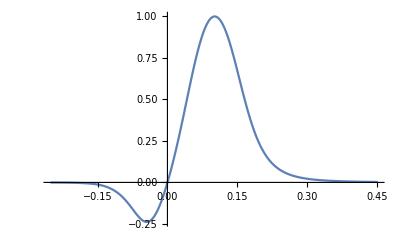

```mathematica
ListLinePlot[gunsol]
```

```mathematica
linacsol=Import["\\\\apclara1\\jkj62\\Online-Model\\MasterLattice\\Data_Files\\SwissFEL_linac_sols.dat"]
```

{{-0.75,0.},{-0.7496,1.85634×10^-6},{-0.7492,3.72142×10^-6},{-0.7488,5.59672×10^-6},{-0.7484,7.48137×10^-6},{-0.748,9.37563×10^-6},{-0.7476,0.0000112795},{-0.7472,0.000013193},{-0.7468,0.0000151162},{-0.7464,0.0000170487},{-0.746,0.0000189915},{-0.7456,0.0000209441},{-0.7452,0.0000229065},{-0.7448,0.0000248791},{-0.7444,0.0000268615},3722,{0.7448,0.0000244454},{0.7452,0.0000224543},{0.7456,0.000020473},{0.746,0.0000185019},{0.7464,0.0000165412},{0.7468,0.0000145894},{0.7472,0.0000126486},{0.7476,0.0000107167},{0.748,8.79477×10^-6},{0.7484,6.88218×10^-6},{0.7488,4.97956×10^-6},{0.7492,3.08679×10^-6},{0.7496,1.20289×10^-6},{0.75,0.}}
 |  |  |  |

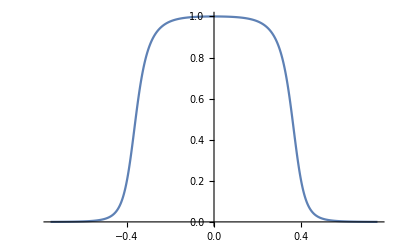

```mathematica
ListLinePlot[linacsol]
```